{1,2 x,-2+4 x^2,-12 x+8 x^3,12-48 x^2+16 x^4,120 x-160 x^3+32 x^5,-120+720 x^2-480 x^4+64 x^6,-1680 x+3360 x^3-1344 x^5+128 x^7,1680-13440 x^2+13440 x^4-3584 x^6+256 x^8,30240 x-80640 x^3+48384 x^5-9216 x^7+512 x^9}

{1,2 x,4 x^2-2,8 x^3-12 x,16 x^4-48 x^2+12,32 x^5-160 x^3+120 x,64 x^6-480 x^4+720 x^2-120,128 x^7-1344 x^5+3360 x^3-1680 x,256 x^8-3584 x^6+13440 x^4-13440 x^2+1680,512 x^9-9216 x^7+48384 x^5-80640 x^3+30240 x}

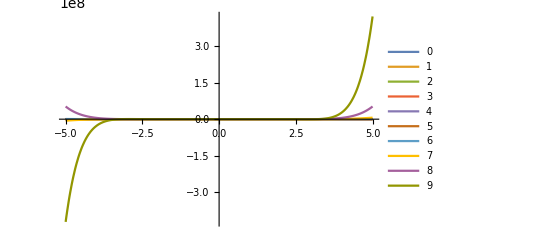

```mathematica
(*Define the Hermite polynomial using the built-in function HermiteH*)
HermitePolynomial[n_,x_]:=HermiteH[n,x]

(*Number of Hermite polynomials to generate*)
numPolynomials=10;

(*Generate Hermite polynomials*)
hermitePolynomials=Table[HermitePolynomial[n,x],{n,0,numPolynomials-1}]

(*Display Hermite polynomials*)
hermitePolynomials//TraditionalForm

(*Plot the Hermite polynomials*)
Plot[Evaluate[hermitePolynomials],{x,-5,5},PlotLegends->Placed[LineLegend[Range[0,numPolynomials-1]],{0.8,0.8}],PlotRange->All,PlotStyle->Table[ColorData[97,"ColorList"][[n]],{n,1,numPolynomials}]]
```

{x^2,2 x^3,x^2 (-2+4 x^2),x^2 (-12 x+8 x^3),x^2 (12-48 x^2+16 x^4)}

{x^2,2 x^3,x^2 (4 x^2-2),x^2 (8 x^3-12 x),x^2 (16 x^4-48 x^2+12)}

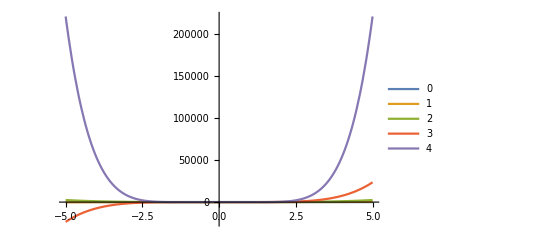

```mathematica
(*Define the Associated Hermite polynomial using a generalized definition*)
AssociatedHermitePolynomial[n_,m_,x_]:=x^m HermiteH[n,x]

(*Number of Hermite polynomials to generate*)
numPolynomials=5;

(*Generate and display the first few Associated Hermite polynomials for a fixed m*)
mValue=2;(*You can change this value to see different associated polynomials*)associatedHermitePolynomials=Table[AssociatedHermitePolynomial[n,mValue,x],{n,0,numPolynomials-1}]

(*Display Associated Hermite polynomials*)
associatedHermitePolynomials//TraditionalForm

(*Plot the Associated Hermite polynomials*)
Plot[Evaluate[associatedHermitePolynomials],{x,-5,5},PlotLegends->Placed[LineLegend[Range[0,numPolynomials-1]],{0.8,0.8}],PlotRange->All,PlotStyle->Table[ColorData[97,"ColorList"][[n]],{n,1,numPolynomials}]]
```

{1,2 x,-2+4 x^2,-12 x+8 x^3,12-48 x^2+16 x^4}

{1,2 x,4 x^2-2,8 x^3-12 x,16 x^4-48 x^2+12}

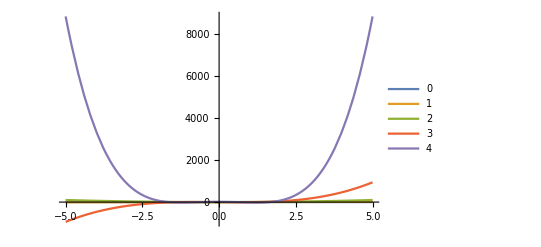

```mathematica
(*Define the physicist's Hermite polynomial using the built-in HermiteH function*)
PhysicistsHermitePolynomial[n_,x_]:=HermiteH[n,x]

(*Number of Hermite polynomials to generate*)
numPolynomials=5;

(*Generate physicist's Hermite polynomials*)
physicistsHermitePolynomials=Table[PhysicistsHermitePolynomial[n,x],{n,0,numPolynomials-1}]

(*Display physicist's Hermite polynomials*)
physicistsHermitePolynomials//TraditionalForm

(*Plot the physicist's Hermite polynomials*)
Plot[Evaluate[physicistsHermitePolynomials],{x,-5,5},PlotLegends->Placed[LineLegend[Range[0,numPolynomials-1]],{0.8,0.8}],PlotRange->All,PlotStyle->Table[ColorData[97,"ColorList"][[n]],{n,1,numPolynomials}]]
```

```mathematica
(*Define the probabilist's Hermite polynomial using HermiteH with a normalization factor*)
ProbabilistsHermitePolynomial[n_,x_]:=(1/Sqrt[2]^n) HermiteH[n,x/Sqrt[2]]

(*Number of Hermite polynomials to generate*)
numPolynomials=5;

(*Generate probabilist's Hermite polynomials*)
probabilistsHermitePolynomials=Table[ProbabilistsHermitePolynomial[n,x],{n,0,numPolynomials-1}]

(*Display probabilist's Hermite polynomials*)
probabilistsHermitePolynomials//TraditionalForm

(*Plot the probabilist's Hermite polynomials*)
Plot[Evaluate[probabilistsHermitePolynomials],{x,-10,10},PlotLegends->Placed[LineLegend[Range[0,numPolynomials-1]],{1.0,1.0}],PlotRange->All,PlotStyle->Table[ColorData[100,"ColorList"][[n]],{n,1,numPolynomials}]]
```

{1,x,1/2 (-2+2 x^2),(-6 √2 x+2 √2 x^3)/(2 √2),1/4 (12-24 x^2+4 x^4)}

{1,x,1/2 (2 x^2-2),(2 √2 x^3-6 √2 x)/(2 √2),1/4 (4 x^4-24 x^2+12)}

-Graphics-

{1,x,1/2 (-2+2 x^2),(-6 √2 x+2 √2 x^3)/(2 √2),1/4 (12-24 x^2+4 x^4),(60 √2 x-40 √2 x^3+4 √2 x^5)/(4 √2),1/8 (-120+360 x^2-120 x^4+8 x^6),(-840 √2 x+840 √2 x^3-168 √2 x^5+8 √2 x^7)/(8 √2),1/16 (1680-6720 x^2+3360 x^4-448 x^6+16 x^8),(15120 √2 x-20160 √2 x^3+6048 √2 x^5-576 √2 x^7+16 √2 x^9)/(16 √2)}

{1,x,1/2 (2 x^2-2),(2 √2 x^3-6 √2 x)/(2 √2),1/4 (4 x^4-24 x^2+12),(4 √2 x^5-40 √2 x^3+60 √2 x)/(4 √2),1/8 (8 x^6-120 x^4+360 x^2-120),(8 √2 x^7-168 √2 x^5+840 √2 x^3-840 √2 x)/(8 √2),1/16 (16 x^8-448 x^6+3360 x^4-6720 x^2+1680),(16 √2 x^9-576 √2 x^7+6048 √2 x^5-20160 √2 x^3+15120 √2 x)/(16 √2)}

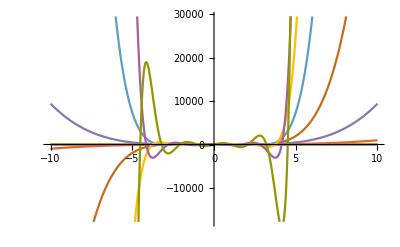

```mathematica
(*Define the probabilist's Hermite polynomial using HermiteH with a normalization factor*)
ProbabilistsHermitePolynomial[n_,x_]:=(1/Sqrt[2]^n) HermiteH[n,x/Sqrt[2]]

(*Number of Hermite polynomials to generate*)
numPolynomials=10;

(*Generate probabilist's Hermite polynomials*)
probabilistsHermitePolynomials=Table[ProbabilistsHermitePolynomial[n,x],{n,0,numPolynomials-1}]

(*Display probabilist's Hermite polynomials*)
probabilistsHermitePolynomials//TraditionalForm

(*Plot the probabilist's Hermite polynomials*)
Plot[Evaluate[probabilistsHermitePolynomials],{x,-10,10}]
```

{1,1-x,1/2 (2-4 x+x^2),1/6 (6-18 x+9 x^2-x^3),1/24 (24-96 x+72 x^2-16 x^3+x^4)}

{1,1-x,1/2 (x^2-4 x+2),1/6 (-x^3+9 x^2-18 x+6),1/24 (x^4-16 x^3+72 x^2-96 x+24)}

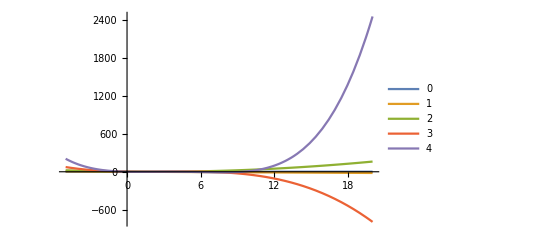

```mathematica
(*Define the Laguerre polynomial using the built-in function LaguerreL*)
LaguerrePolynomial[n_,x_]:=LaguerreL[n,x]

(*Number of Laguerre polynomials to generate*)
numPolynomials=5;

(*Generate Laguerre polynomials*)
laguerrePolynomials=Table[LaguerrePolynomial[n,x],{n,0,numPolynomials-1}]

(*Display Laguerre polynomials*)
laguerrePolynomials//TraditionalForm

(*Plot the Laguerre polynomials*)
Plot[Evaluate[laguerrePolynomials],{x,-5,20},PlotLegends->Placed[LineLegend[Range[0,numPolynomials-1]],{0.5,0.5}],PlotRange->All,PlotStyle->Table[ColorData[97,"ColorList"][[n]],{n,1,numPolynomials}]]
```

{1,3-x,1/2 (12-8 x+x^2),1/6 (60-60 x+15 x^2-x^3),1/24 (360-480 x+180 x^2-24 x^3+x^4)}

{1,3-x,1/2 (x^2-8 x+12),1/6 (-x^3+15 x^2-60 x+60),1/24 (x^4-24 x^3+180 x^2-480 x+360)}

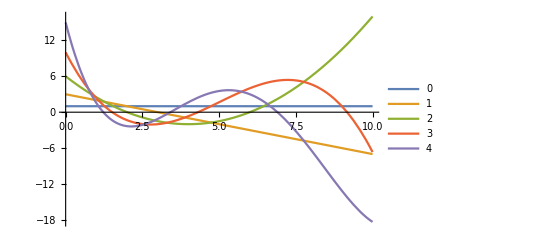

```mathematica
(*Define the associated Laguerre polynomial using the built-in function LaguerreL*)
AssociatedLaguerrePolynomial[n_,k_,x_]:=LaguerreL[n,k,x]

(*Number of Laguerre polynomials to generate*)
numPolynomials=5;

(*Value of k for associated Laguerre polynomials*)
kValue=2;(*You can change this value to see different associated polynomials*)(*Generate associated Laguerre polynomials*)associatedLaguerrePolynomials=Table[AssociatedLaguerrePolynomial[n,kValue,x],{n,0,numPolynomials-1}]

(*Display associated Laguerre polynomials*)
associatedLaguerrePolynomials//TraditionalForm

(*Plot the associated Laguerre polynomials*)
Plot[Evaluate[associatedLaguerrePolynomials],{x,0,10},PlotLegends->Placed[LineLegend[Range[0,numPolynomials-1]],{0.8,0.8}],PlotRange->All,PlotStyle->Table[ColorData[97,"ColorList"][[n]],{n,1,numPolynomials}]]
```

{-(√2 Cos[x])/(π √x),-(√2 √(x^2) (Cos[x]+x Sin[x]))/(π x^(3/2)),(√2 ((-3+x^2) Cos[x]-3 x Sin[x]))/(π √x),(√2 √(x^2) (3 (-5+2 x^2) Cos[x]+x (-15+x^2) Sin[x]))/(π x^(3/2)),-(√2 ((105-45 x^2+x^4) Cos[x]+5 x (21-2 x^2) Sin[x]))/(π √x)}

{-(√2 cos(x))/(π √x),-(√2 √(x^2) (x sin(x)+cos(x)))/(π x^(3/2)),(√2 ((x^2-3) cos(x)-3 x sin(x)))/(π √x),(√2 √(x^2) (x (x^2-15) sin(x)+3 (2 x^2-5) cos(x)))/(π x^(3/2)),-(√2 (5 x (21-2 x^2) sin(x)+(x^4-45 x^2+105) cos(x)))/(π √x)}

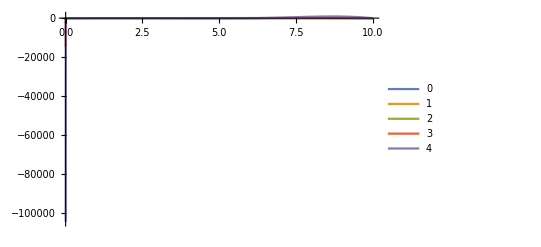

```mathematica
(*Define the Bessel polynomial using the built-in function BesselY*)
BesselPolynomial[n_,x_]:=Simplify[(x^2)^(n/2)*BesselY[n+1/2,x]/Sqrt[π]]

(*Number of Bessel polynomials to generate*)
numPolynomials=5;

(*Generate Bessel polynomials*)
besselPolynomials=Table[BesselPolynomial[n,x],{n,0,numPolynomials-1}]

(*Display Bessel polynomials*)
besselPolynomials//TraditionalForm

(*Plot the Bessel polynomials*)
Plot[Evaluate[besselPolynomials],{x,0,10},PlotLegends->Placed[LineLegend[Range[0,numPolynomials-1]],{0.8,0.8}],PlotRange->All,PlotStyle->Table[ColorData[97,"ColorList"][[n]],{n,1,numPolynomials}]]
```

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4)}

{1,x,1/2 (3 x^2-1),1/2 (5 x^3-3 x),1/8 (35 x^4-30 x^2+3)}

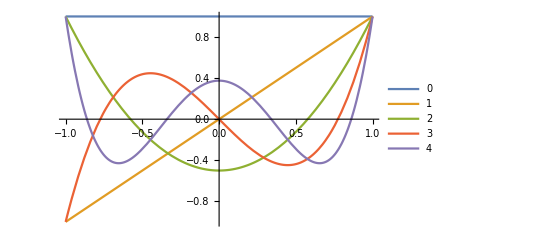

```mathematica
(*Define the Legendre polynomial using the built-in function LegendreP*)
LegendrePolynomial[n_,x_]:=LegendreP[n,x]

(*Number of Legendre polynomials to generate*)
numPolynomials=5;

(*Generate Legendre polynomials*)
legendrePolynomials=Table[LegendrePolynomial[n,x],{n,0,numPolynomials-1}]

(*Display Legendre polynomials*)
legendrePolynomials//TraditionalForm

(*Plot the Legendre polynomials*)
Plot[Evaluate[legendrePolynomials],{x,-1,1},PlotLegends->Placed[LineLegend[Range[0,numPolynomials-1]],{0.8,0.8}],PlotRange->All,PlotStyle->Table[ColorData[97,"ColorList"][[n]],{n,1,numPolynomials}]]
```

{-3 (-1+x^2),-15 x (-1+x^2),-15/2 (-1+x^2) (-1+7 x^2),-105/2 (-1+x^2) (-x+3 x^3),-105/8 (-1+x^2) (1-18 x^2+33 x^4)}

{-3 (x^2-1),-15 x (x^2-1),-15/2 (x^2-1) (7 x^2-1),-105/2 (x^2-1) (3 x^3-x),-105/8 (x^2-1) (33 x^4-18 x^2+1)}

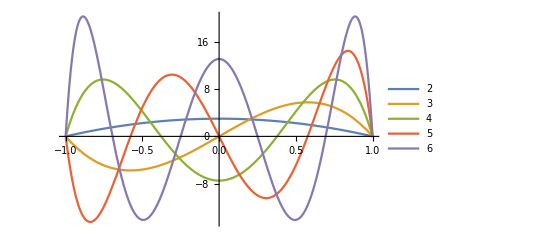

```mathematica
(*Define the associated Legendre polynomial using the built-in function LegendreP*)
AssociatedLegendrePolynomial[n_,m_,x_]:=LegendreP[n,m,x]

(*Number of Legendre polynomials to generate*)
numPolynomials=5;

(*Value of m for associated Legendre polynomials*)
mValue=2;(*You can change this value to see different associated polynomials*)(*Generate associated Legendre polynomials*)associatedLegendrePolynomials=Table[AssociatedLegendrePolynomial[n,mValue,x],{n,mValue,numPolynomials+mValue-1}]

(*Display associated Legendre polynomials*)
associatedLegendrePolynomials//TraditionalForm

(*Plot the associated Legendre polynomials*)
Plot[Evaluate[associatedLegendrePolynomials],{x,-1,1},PlotLegends->Placed[LineLegend[Range[mValue,numPolynomials+mValue-1]],{0.8,0.8}],PlotRange->All,PlotStyle->Table[ColorData[97,"ColorList"][[n]],{n,1,numPolynomials}]]
```